## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulum.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[ParentDirectory[]]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/6- Newton Sinplifikatua/Packages/

```mathematica
Get["RKGNEWTON`",Path->MyPackageDirectory];
Get["DoublePendulum`",Path->MyPackageDirectory];
```

### Install math-Gauss

```mathematica
Run["echo '#define PREC 1'>prec.h"];
Run["make math-Gauss"];
link1=Install["math-Gauss"];
```

LinkOpen::linke: Could not find MathLink executable.

### Install quad-Gauss

```mathematica
Run["echo '#define PREC 2'>prec.h"];
Run["make quad-Gauss"];
link2=Install["quad-Gauss"];
```

LinkOpen::linke: Could not find MathLink executable.

### Install math-GaussPar

```mathematica
Run["echo '#define PREC 1'>prec.h"];
Run["make math-GaussPar"];
link3=Install["math-GaussPar"];
```

LinkOpen::linke: Could not find MathLink executable.

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Blue;
StyleMachine=Orange;
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

### Auxiliary functions

```mathematica
Pert[e0_,k_]:={e0*(k*RandomReal[{-1,1}])};
```

```mathematica
FunMeanHerr[outAll_, outBAll_, nstat_,nout_,HAM_,parameters_,prec_]:=
Module[{i,Ham0, Hamerr,Error, SHamerr=Array[0 &,nout],
             SError=Array[0 &,nout],
             EndHam=Array[0&,nstat],outA,outB},
For[i=1, i≤ nstat,i++,
  outA=outAll[[i]];
  outB=outBAll[[i]];
  Ham0 = HAM[First[outA],parameters,prec];
         Hamerr = Map[HAM[#,parameters,prec]/Ham0-1&,outA];
  EndHam[[i]]=Last[Hamerr];
  SHamerr=SHamerr+Abs[Hamerr];
  Error = MapThread[ErrorPos2[#1,#2,prec]&,{outB, outA}];
  SError=SError+Abs[Error];
];
{SHamerr/nstat,SError/nstat ,EndHam}
]
```

```mathematica
FunHerr[outAll_, nstat_,nout_,HAM_,parameters_,prec_,step_Integer]:=
Module[{i,Ham0, Hamerr,Hamerrdif,Error,outA},
Hamerrdif={};
For[i=1, i≤ nstat,i++,
  outA=outAll[[i]];
  Ham0 = HAM[First[outA],parameters,prec];
         Hamerr=Map[HAM[#,parameters,prec]/Ham0-1&,outA];
  Hamerr=Map[First,Partition[Hamerr,step]];
  Hamerrdif = Join[Hamerrdif,Drop[Hamerr,1]-Drop[Hamerr,-1]];
];
Hamerrdif
]
```

```mathematica
FunMeanEst[outAll_,outBAll_,nstat_,nout_,neq_]:=
Module[{i,outA,outB,
             est,estQ,meanEst,desvEst,Error,
             Qty,meanQty,desvQty,
             Sout=Partition[Array[0 &,(nout*(neq/2))],neq/2],
             S2out=Partition[Array[0 &,(nout*(neq/2))],neq/2],
             SEstQty=Array[0 &,nout],
             S2EstQty=Array[0 &,nout]},

For[i=1, i≤ nstat,i++,
outA=outAll[[i]];
outB=outBAll[[i]];
est=Take[outA, All,{2neq+2,3neq+1}];
estQ=Take[est,All,{1,neq/2}];
Sout=Sout+estQ;
S2out=S2out+estQ^2;
Error = MapThread[ErrorPos2[#1,#2,prec]&,{outB, outA}];
Qty=Log[10,Map[Norm,estQ]/Error];
SEstQty=SEstQty+Qty;
S2EstQty=S2EstQty+Qty^2;
];

meanEst=Sout/nstat;
desvEst=Sqrt[S2out/nstat-meanEst^2];
meanQty=SEstQty/nstat;
desvQty=Sqrt[S2EstQty/nstat-meanQty^2];
{Map[Norm,meanEst],Map[Norm,desvEst],meanQty,desvQty}
];
```

## Filenames

```mathematica
myDirectory="Data/";
```

```mathematica
outNS6={"outNS61.bin","outNS62.bin","outNS63.bin","outNS64.bin","outNS65.bin","outNS66.bin","outNS67.bin"};
outNS8={"outNS81.bin","outNS82.bin","outNS83.bin","outNS84.bin","outNS85.bin","outNS86.bin","outNS87.bin"};
outNS16={"outNS161.bin","outNS162.bin","outNS163.bin","outNS164.bin","outNS165.bin","outNS166.bin","outNS167.bin"};
outNS6B={"outNS61B.bin","outNS62B.bin","outNS63B.bin","outNS64B.bin","outNS65B.bin","outNS66B.bin","outNS67B.bin"};
outNS8B={"outNS81B.bin","outNS82B.bin","outNS83B.bin","outNS84B.bin","outNS85B.bin","outNS86B.bin","outNS87B.bin"};
outNS16B={"outNS161B.bin","outNS162B.bin","outNS163B.bin","outNS164B.bin","outNS165B.bin","outNS166B.bin","outNS167B.bin"};
```

```mathematica
filey0=NotebookDirectory[]<>myDirectory<>"Datay0.bin";
fileNS6=Table[NotebookDirectory[]<>myDirectory<>outNS6[[i]],{i,Length[outNS6]}];
fileNS8=Table[NotebookDirectory[]<>myDirectory<>outNS8[[i]],{i,Length[outNS8]}];
fileNS16=Table[NotebookDirectory[]<>myDirectory<>outNS16[[i]],{i,Length[outNS16]}];
fileNS6B=Table[NotebookDirectory[]<>myDirectory<>outNS6B[[i]],{i,Length[outNS6B]}];
fileNS8B=Table[NotebookDirectory[]<>myDirectory<>outNS8B[[i]],{i,Length[outNS8B]}];
fileNS16B=Table[NotebookDirectory[]<>myDirectory<>outNS16B[[i]],{i,Length[outNS16B]}];
```

## Parameters (non-chaotic initial values)

### Problem parameters and initial values.

```mathematica
prec=100;
n=2;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;

C1=l2^2*m2;
C2=l1^2(m1+m2);
C3=-2 l1 l2 l2;
C4=2l1^2l2^2*m2*m1;
C5=2m1^2l2^2*m2^2;
C6=g l1 (m1+m2);
C7=g l2 m2;

Q10=(11/10);Q20=0;
P10=0;P20=27746/10000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7};
pint={0,0};
```

```mathematica
u0
```

{11/10,0,0,13873/5000}

```mathematica
parameters
```

{1,2,-2,2,2,98/5,49/5}

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
u0
```

{11/10,0,0,13873/5000}

```mathematica
N[ee0,20]
```

{-8.8817841970012523234×10^-17,0,0,4.476419235288631171×10^-17}

### Integration parameters.

```mathematica
t0=0.;tend=2.^4 ;(*2.^(10)*)
h=2.^(-7);
h0=2.^(-7);
hs6={h0/8,h0/4,h0/2,h0,2*h0,4*h0,8*h0};
hs8=hs6*8/6;
hs16=hs6*16/6;
sampling=1; (*2^7*)
```

```mathematica
codfun0=1; (*OdePendulum*)
codfunX=11; (*OdePendulumX*)
approx = 1; 
ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

2048.

```mathematica
nsteps6=(tend-t0)/hs6;
nouts6=Ceiling[nsteps6/sampling]
nsteps8=(tend-t0)/hs8;
nouts8=Ceiling[nsteps8/sampling]
nsteps16=(tend-t0)/hs16;
nouts16=Ceiling[nsteps16/sampling]
```

{16384,8192,4096,2048,1024,512,256}

{12288,6144,3072,1536,768,384,192}

{6144,3072,1536,768,384,192,96}

### RKG parameters

```mathematica
neq=4;
prec=100;
HAM=DoublePendulumHam2;
```

## Analisis-0 NS6

```mathematica
nstat=10;
nk=7; 
dd1= (2neq+1);
dd2= (3neq+1);
outA=tpA=MeanHamA=MeanErrA=EndHamA=Array[{}&,nk];
InPutfile=fileNS6B;
nout=nouts6+1
```

{16385,8193,4097,2049,1025,513,257}

```mathematica
For[k=1, k≤nk, k++,

noutA=nout[[k]];
s=InPutfile[[k]];
outA[[k]]=SetPrecision[ArrayReshape[BinaryReadList[s,"Real128"],{nstat,noutA,dd1}],prec];
tpA[[k]]=Flatten[Take[outA[[k]][[1]],All,{1,1}]];

{MeanHamA[[k]],MeanErrA[[k]],EndHamA[[k]]}=FunMeanHerr[outA[[k]],outA[[k]], nstat,noutA,HAM, parameters,prec] ;

]
```

```mathematica
nout
```

{16385,8193,4097,2049,1025,513,257}

```mathematica
Union[Flatten[Table[{Length[outA[[k]]],Length[outA[[k]][[n]]]},{k,nk},{n,nstat}],1]]
```

{{10,257},{10,513},{10,1025},{10,2049},{10,4097},{10,8193},{10,16385}}

```mathematica
Table[Take[outA[[1]][[n]],1]//N,{n,nstat}]
```

{{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}}}

```mathematica
Table[Take[outA[[1]][[n]],-2]//N,{n,nstat}]
```

{{{15.999,0.229896,0.95436,-1.04038,3.41921,-4.13774×10^-36,-2.25695×10^-35,-3.46066×10^-35,-8.27548×10^-36},{16.,0.227461,0.959518,-1.05328,3.41995,-4.13774×10^-36,-1.35417×10^-35,-3.46066×10^-35,1.6551×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,-8.65164×10^-36,4.66436×10^-35,8.27548×10^-35,-7.14701×10^-35},{16.,0.227461,0.959518,-1.05328,3.41995,9.78011×10^-36,4.36344×10^-35,3.46066×10^-35,-8.35071×10^-35}},{{15.999,0.229896,0.95436,-1.04038,3.41921,-7.14701×10^-36,-1.35417×10^-35,-1.6551×10^-35,1.6156×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,-7.14701×10^-36,-4.36344×10^-35,2.55788×10^-35,1.66074×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,6.77085×10^-36,1.05324×10^-35,-4.36344×10^-35,-1.88079×10^-37},{16.,0.227461,0.959518,-1.05328,3.41995,3.76158×10^-37,1.6551×10^-35,-1.35417×10^-35,-1.44633×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,1.12847×10^-35,-3.15973×10^-35,2.8588×10^-35,1.59491×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,3.76158×10^-36,-6.01853×10^-36,4.96529×10^-35,-1.6551×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,-1.05324×10^-35,1.73033×10^-35,3.15973×10^-35,-9.40395×10^-35},{16.,0.227461,0.959518,-1.05328,3.41995,-9.40395×10^-36,2.33218×10^-35,4.36344×10^-35,-1.51216×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,6.01853×10^-36,2.03125×10^-35,8.12502×10^-35,-1.14352×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,7.52316×10^-37,-3.98728×10^-35,-6.01853×10^-35,-1.80556×10^-35}},{{15.999,0.229896,0.95436,-1.04038,3.41921,6.01853×10^-36,2.03125×10^-35,8.12502×10^-35,-1.14352×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,7.52316×10^-37,-3.98728×10^-35,-6.01853×10^-35,-1.80556×10^-35}},{{15.999,0.229896,0.95436,-1.04038,3.41921,-1.09086×10^-35,-2.40741×10^-35,9.32872×10^-35,1.64757×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,-3.38542×10^-36,3.31019×10^-35,4.5139×10^-35,-1.40683×10^-34}},{{15.999,0.229896,0.95436,-1.04038,3.41921,-9.0278×10^-36,7.52316×10^-37,-7.52316×10^-36,-1.68425×10^-34},{16.,0.227461,0.959518,-1.05328,3.41995,1.05324×10^-35,-4.43867×10^-35,-3.76158×10^-35,1.86669×10^-34}}}

### Graphics-I (Energia)

```mathematica
MeanHamAdata =Array[{}&,nk];
For [k=1, k≤nk,k++,
MeanHamAdata[[k]] = Transpose[{tpA[[k]],MeanHamA[[k]]}];
]
(*MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];*)
```

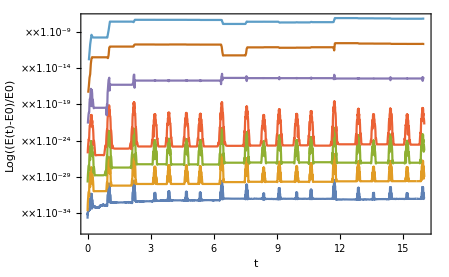

```mathematica
plotHS6=ListLogPlot[Table[MeanHamAdata[[k]],{k,nk}],AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
(*PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
```

```mathematica
Export[NotebookDirectory[]<>myDirectory<>"plotHS6.pdf",Show[plotHS6] ];
```

## Analisis-0 NS8

```mathematica
nstat=10;
nk=7; 
dd1= (2neq+1);
dd2= (3neq+1);
outA=tpA=MeanHamA=MeanErrA=EndHamA=Array[{}&,nk];
InPutfile=fileNS8B;
nout=nouts8+2
```

{12290,6146,3074,1538,770,386,194}

```mathematica
For[k=1, k≤nk, k++,

noutA=nout[[k]];
s=InPutfile[[k]];
outA[[k]]=SetPrecision[ArrayReshape[BinaryReadList[s,"Real128"],{nstat,noutA,dd1}],prec];
tpA[[k]]=Flatten[Take[outA[[k]][[1]],All,{1,1}]];

{MeanHamA[[k]],MeanErrA[[k]],EndHamA[[k]]}=FunMeanHerr[outA[[k]],outA[[k]], nstat,noutA,HAM, parameters,prec] ;

]
```

```mathematica
nout
```

{12290,6146,3074,1538,770,386,194}

```mathematica
Union[Flatten[Table[{Length[outA[[k]]],Length[outA[[k]][[n]]]},{k,nk},{n,nstat}],1]]
```

{{10,194},{10,386},{10,770},{10,1538},{10,3074},{10,6146},{10,12290}}

```mathematica
Table[Take[outA[[3]][[n]],1]//N,{n,nstat}]
```

{{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}}}

```mathematica
Table[Take[outA[[1]][[n]],-2]//N,{n,nstat}]
```

{{{16.,0.227461,0.959518,-1.05328,3.41995,5.26621×10^-36,1.88079×10^-35,-4.81482×10^-35,3.31019×10^-35},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,5.26621×10^-36,-1.50463×10^-36,4.81482×10^-35,-3.00927×10^-36}},{{16.,0.227461,0.959518,-1.05328,3.41995,-7.52316×10^-37,9.78011×10^-36,-1.80556×10^-35,1.38426×10^-34},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,9.78011×10^-36,-6.01853×10^-36,7.82409×10^-35,-1.92593×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-1.20371×10^-35,3.76158×10^-35,1.20371×10^-35,1.51216×10^-34},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,-6.01853×10^-36,7.52316×10^-36,-8.42594×10^-35,-1.61748×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,1.12847×10^-35,-3.46066×10^-35,-4.21297×10^-35,-7.6172×10^-35},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,-4.89006×10^-36,-7.52316×10^-36,-1.80556×10^-35,-5.51072×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,-3.38542×10^-36,-2.70834×10^-35,-6.01853×10^-36,-4.0437×10^-35},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,4.13774×10^-36,4.5139×10^-35,6.01853×10^-36,-1.72845×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-8.65164×10^-36,1.12847×10^-35,6.01853×10^-36,-8.83972×10^-36},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,6.39469×10^-36,-1.27894×10^-35,4.21297×10^-35,-1.7134×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-6.39469×10^-36,2.25695×10^-35,-7.22224×10^-35,9.78011×10^-36},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,-7.89932×10^-36,2.70834×10^-35,9.62965×10^-35,-1.90336×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-6.39469×10^-36,2.25695×10^-35,-7.22224×10^-35,9.78011×10^-36},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,-7.89932×10^-36,2.70834×10^-35,9.62965×10^-35,-1.90336×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,7.89932×10^-36,-3.68635×10^-35,-6.31946×10^-35,-1.36922×10^-34},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,6.77085×10^-36,4.73959×10^-35,1.50463×10^-35,-3.46066×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,9.0278×10^-36,4.58913×10^-35,-3.00927×10^-36,-6.35707×10^-35},{1.09148×10^-11,0.224237,0.966358,-1.07038,3.42086,9.0278×10^-36,-1.05324×10^-35,8.12502×10^-35,1.13976×10^-34}}}

### Graphics-I (Energia)

```mathematica
nk=7;
```

```mathematica
MeanHamAdata =Array[{}&,nk];
For [k=1, k≤nk,k++,
MeanHamAdata[[k]] =Drop[ Transpose[{tpA[[k]],MeanHamA[[k]]}],-1];
]
(*MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];*)
```

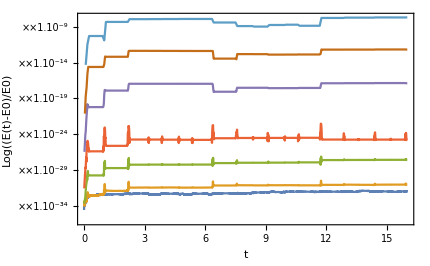

```mathematica
plotHS8=ListLogPlot[Table[MeanHamAdata[[k]],{k,1,nk}],AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
(*PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
```

```mathematica
Export[NotebookDirectory[]<>myDirectory<>"plotHS8.pdf",Show[plotHS8] ];
```

## Analisis-0 NS16

```mathematica
nstat=10;
nk=5; 
dd1= (2neq+1);
dd2= (3neq+1);
outA=tpA=MeanHamA=MeanErrA=EndHamA=Array[{}&,nk];
InPutfile=fileNS16B;
nout=nouts16+2
```

{6146,3074,1538,770,386,194,98}

```mathematica
For[k=1, k≤nk, k++,

noutA=nout[[k]];
s=InPutfile[[k]];
outA[[k]]=SetPrecision[ArrayReshape[BinaryReadList[s,"Real128"],{nstat,noutA,dd1}],prec];
tpA[[k]]=Flatten[Take[outA[[k]][[1]],All,{1,1}]];

{MeanHamA[[k]],MeanErrA[[k]],EndHamA[[k]]}=FunMeanHerr[outA[[k]],outA[[k]], nstat,noutA,HAM, parameters,prec] ;

]
```

```mathematica
nout
```

{6146,3074,1538,770,386,194,98}

```mathematica
Union[Flatten[Table[{Length[outA[[k]]],Length[outA[[k]][[n]]]},{k,nk},{n,nstat}],1]]
```

{{10,386},{10,770},{10,1538},{10,3074},{10,6146}}

```mathematica
Table[Take[outA[[1]][[n]],1]//N,{n,nstat}]
```

{{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}},{{0.,1.1,0.,0.,2.7746,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308,1.1125369292536×10^-308}}}

```mathematica
Table[Take[outA[[1]][[n]],-2]//N,{n,nstat}]
```

{{{16.,0.227461,0.959518,-1.05328,3.41995,-1.50463×10^-36,-2.25695×10^-35,-4.81482×10^-35,-5.64237×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,4.5139×10^-36,4.5139×10^-35,4.81482×10^-35,1.18114×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-1.50463×10^-36,-6.01853×10^-36,4.21297×10^-35,4.13774×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,-7.52316×10^-36,3.00927×10^-36,4.81482×10^-35,1.39931×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-6.77085×10^-36,-4.81482×10^-35,0.,-5.49191×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,1.50463×10^-36,6.01853×10^-36,7.82409×10^-35,3.12211×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,3.00927×10^-36,1.6551×10^-35,-6.01853×10^-35,4.17536×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,-1.20371×10^-35,3.91205×10^-35,9.62965×10^-35,1.3805×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,7.52316×10^-37,-1.50463×10^-35,3.61112×10^-35,-4.10012×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,-1.20371×10^-35,-1.05324×10^-35,-6.01853×10^-35,-7.10939×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,3.00927×10^-36,1.80556×10^-35,6.01853×10^-36,3.64873×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,1.05324×10^-35,-1.05324×10^-35,-4.21297×10^-35,9.21588×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,1.20371×10^-35,-4.21297×10^-35,7.22224×10^-35,3.27258×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,9.78011×10^-36,4.5139×10^-35,-6.01853×10^-35,-1.86951×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,1.20371×10^-35,-4.21297×10^-35,7.22224×10^-35,3.27258×10^-35},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,9.78011×10^-36,4.5139×10^-35,-6.01853×10^-35,-1.86951×10^-34}},{{16.,0.227461,0.959518,-1.05328,3.41995,-7.52316×10^-37,4.36344×10^-35,1.80556×10^-35,1.63253×10^-34},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,-2.25695×10^-36,1.35417×10^-35,-3.00927×10^-35,4.89006×10^-35}},{{16.,0.227461,0.959518,-1.05328,3.41995,5.26621×10^-36,1.50463×10^-36,6.01853×10^-36,-1.44445×10^-34},{5.45786×10^-12,0.22104,0.973158,-1.08736,3.42168,-2.25695×10^-36,-1.20371×10^-35,2.40741×10^-35,1.6551×10^-34}}}

### Graphics-I (Energia)

```mathematica
MeanHamAdata =Array[{}&,nk];
For [k=1, k≤nk,k++,
MeanHamAdata[[k]] = Drop[Transpose[{tpA[[k]],MeanHamA[[k]]}],-1];
]
(*MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];*)
```

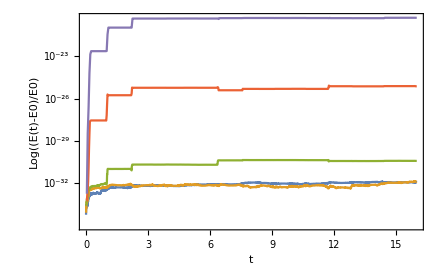

```mathematica
plotHS16=ListLogPlot[Table[MeanHamAdata[[k]],{k,1,nk}],AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
(*PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
```

```mathematica
Export[NotebookDirectory[]<>myDirectory<>"plotHS16.pdf",Show[plotHS16] ];
```